## Counting numbers

```mathematica
Clear[CountOccurrences];
CountOccurrences[list_]:=Block[{res,cur,cnt},
res={};
cur=list[[1]];
cnt=0;
Table[If[l==cur,cnt=cnt+1,AppendTo[res,{cur,cnt}];cur=l;cnt=1];,{l,list}]; 
AppendTo[res,{cur,cnt}];
res
];
```

```mathematica
Clear[NumberOfNumbers]
NumberOfNumbers[1]:=IntegerDigits[1];
NumberOfNumbers[n_Integer]:=NumberOfNumbers[n]=Flatten[CountOccurrences[NumberOfNumbers[n-1]]]
```

```mathematica
NumberOfNumbers[1]
```

{1}

```mathematica
NumberOfNumbers[2]
```

{1,1}

```mathematica
NumberOfNumbers[3]
```

{1,2}

```mathematica
NumberOfNumbers[4]
```

{1,1,2,1}

```mathematica
NumberOfNumbers[10]
```

{1,1,2,2,1,1,3,1,1,3,2,1,1,1,3,1,1,2,3,1}

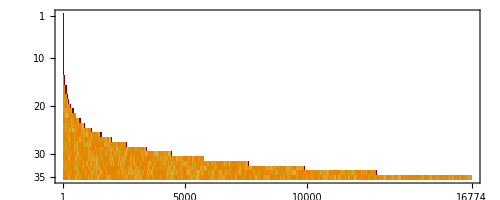

```mathematica
MatrixPlot[Table[NumberOfNumbers[i],{i,Range[35]}]]
```